```mathematica
Clear["`*"]
```

```mathematica
<<PlotLegends`
```

# Spencer Lyon

## Physics 330

Lab 2

## P2.1

2

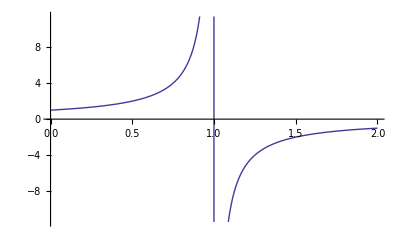

```mathematica
p = 2;
y2 = y[t]/. DSolve[{D[y[t],t] == y[t]^p, y[0]==1}, y[t],t][[1]];
Plot[y2, {t , 0, 2}]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

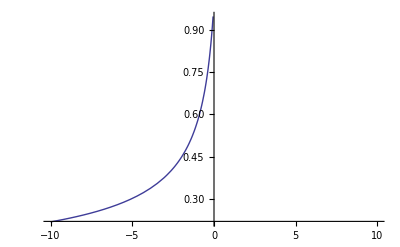

```mathematica
p = 3;
y3 = y[t]/. DSolve[{D[y[t],t] == y[t]^p, y[0]==1}, y[t],t][[1]];
Plot[y3, {t , -10, 10}]
```

```mathematica
Solve[Pc/P == 1 - ( 1 + β * d) * Exp[ - (β * d)], β]//InputForm
```

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

{{β -> (-1 - ProductLog[(-P + Pc)/(E*P)])/d}}

## P2.3

### a.)

{-3/(3 t+1)}

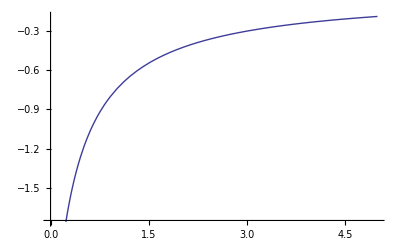

```mathematica
eqnsA = {D[y[t], t ]== y[t]^2, y[0]==-3};
yA = y[t]/.DSolve[eqnsA, y[t],t]
Plot[yA, {t,0,5}]
```

### b.)

1/2 ⅇ^-t (ⅇ^(2 t)+1)

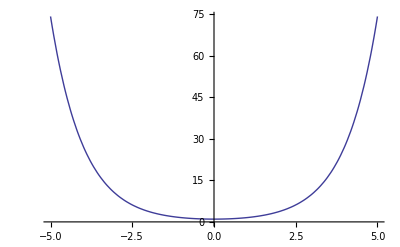

```mathematica
eqnsB = {D[y[t], {t,2} ]== y[t], y[0]==1, y'[0]==0};
yB = y[t]/.DSolve[eqnsB, y[t],t][[1]]
Plot[yB, {t,-5,5}]
```

### c.)

InterpolatingFunction[(-4. | 4.),<>](t)

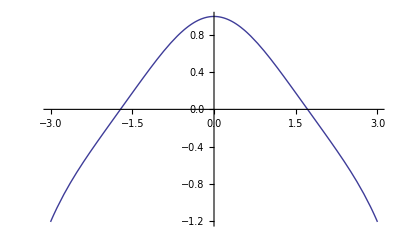

```mathematica
eqnsC = {D[y[t], {t,2} ]== -y[t]^2, y[0]==1, y'[0]==0};
tmin = -4; tmax = 4;
yC = y[t]/.NDSolve[eqnsC, y[t],{t, tmin, tmax}][[1]]
Plot[yC, {t,-3,3}]
```

### d.)

InterpolatingFunction[(-25. | 25.),<>](t)

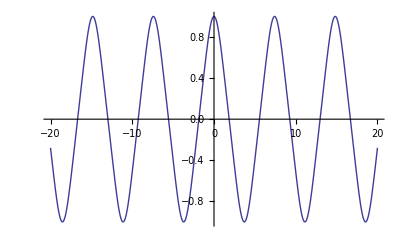

```mathematica
eqnsD = {D[y[t], {t,2} ]== -y[t]^3, y[0]==1, y'[0]==0};
tmin = -25; tmax = 25;
yD = y[t]/.NDSolve[eqnsD, y[t],{t, tmin, tmax}][[1]]
Plot[yD, {t,-20,20}]
```

```mathematica
RecurrenceTable[{a[n+1]==(n/((n - 1/2)(n+1/2)))a[n], a[1]==1},a,{n,1,20}]//N
```

{1.,1.33333,0.711111,0.24381,0.0619199,0.0125091,0.00209942,0.000301456,0.0000378297,4.21632×10^-6,4.22688×10^-7,3.85058×10^-8,3.2144×10^-9,2.47628×10^-10,1.77103×10^-11,1.182×10^-12,7.39471×10^-14,4.35359×10^-15,2.42053×10^-16,1.27485×10^-17}